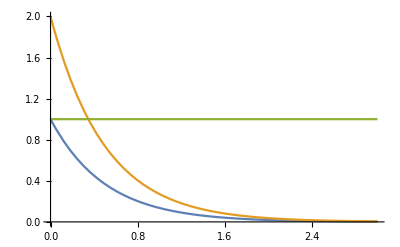

~/Source_Code/nn_scripts/test/analytical/1D_poisson_Ev.dat

~/Source_Code/nn_scripts/test/analytical/1D_poisson_Hv.dat

~/Source_Code/nn_scripts/test/analytical/1D_poisson_Gv.dat

```mathematica
(*1D poisson*)
Ev[r_]:=Exp[-2r]
Hv[r_]:=2 Exp[-2 r]
Gv[r_]:=Hv[r]/(2 Ev[r])
Plot[{Ev[r],Hv[r],Gv[r]},{r,0,3}]
tableUnc=Table[0.0,{r,0.001,3,0.001}];
tableR=Table[r,{r,0.001,3,0.001}];
tableEv=Table[Ev[r],{r,0.001,3,0.001}];
tableHv=Table[Hv[r],{r,0.001,3,0.001}];
tableGv=Table[Gv[r],{r,0.001,3,0.001}];

Export["~/Source_Code/nn_scripts/test/analytical/1D_poisson_Ev.dat",Transpose[{tableR,tableEv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/1D_poisson_Hv.dat",Transpose[{tableR,tableHv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/1D_poisson_Gv.dat",Transpose[{tableR,tableGv,tableUnc}]]
```

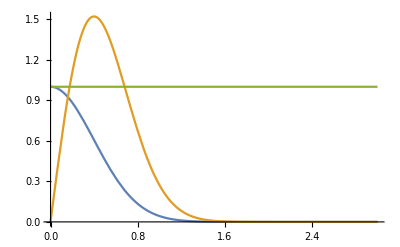

~/Source_Code/nn_scripts/test/analytical/2D_poisson_Ev.dat

~/Source_Code/nn_scripts/test/analytical/2D_poisson_Hv.dat

~/Source_Code/nn_scripts/test/analytical/2D_poisson_Gv.dat

```mathematica
(*2D poisson*)
Ev[r_]:=Exp[-Pi r^2]
Hv[r_]:=2 Pi r Exp[-Pi r^2]
Gv[r_]:=Hv[r]/(2 Pi r Ev[r])
Plot[{Ev[r],Hv[r],Gv[r]},{r,0,3}]
tableUnc=Table[0.0,{r,0.001,3,0.001}];
tableR=Table[r,{r,0.001,3,0.001}];
tableEv=Table[Ev[r],{r,0.001,3,0.001}];
tableHv=Table[Hv[r],{r,0.001,3,0.001}];
tableGv=Table[Gv[r],{r,0.001,3,0.001}];

Export["~/Source_Code/nn_scripts/test/analytical/2D_poisson_Ev.dat",Transpose[{tableR,tableEv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/2D_poisson_Hv.dat",Transpose[{tableR,tableHv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/2D_poisson_Gv.dat",Transpose[{tableR,tableGv,tableUnc}]]
```

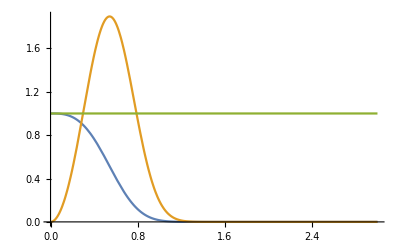

~/Source_Code/nn_scripts/test/analytical/3D_poisson_Ev.dat

~/Source_Code/nn_scripts/test/analytical/3D_poisson_Hv.dat

~/Source_Code/nn_scripts/test/analytical/3D_poisson_Gv.dat

```mathematica
(*3D poisson*)
Ev[r_]:=Exp[-4 Pi/3 r^3]
Hv[r_]:=4 Pi r^2 Exp[-4Pi/3 r^3]
Gv[r_]:=Hv[r]/(4 Pi r^2 Ev[r])
Plot[{Ev[r],Hv[r],Gv[r]},{r,0,3}]
tableUnc=Table[0.0,{r,0.001,3,0.001}];
tableR=Table[r,{r,0.001,3,0.001}];
tableEv=Table[Ev[r],{r,0.001,3,0.001}];
tableHv=Table[Hv[r],{r,0.001,3,0.001}];
tableGv=Table[Gv[r],{r,0.001,3,0.001}];

Export["~/Source_Code/nn_scripts/test/analytical/3D_poisson_Ev.dat",Transpose[{tableR,tableEv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/3D_poisson_Hv.dat",Transpose[{tableR,tableHv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/3D_poisson_Gv.dat",Transpose[{tableR,tableGv,tableUnc}]]
```

1

1/(√2)

-(Piecewise[{{-2 π r, r<1/2}, {-π, r==1/2}, {2/(√(1-1/(4 r^2)))-2 π r-√((-1+4 r^2)/r^2)-(r (8/r-(2 (-1+4 r^2))/r^3))/(2 √((-1+4 r^2)/r^2))+8 r ArcCos[1/(2 r)], 1/2<r<1/(√2)}, {0, True}}])

-Piecewise[{{-2 π r, r<1/2}, {-π, r==1/2}, {2/(√(1-1/(4 r^2)))-2 π r-√((-1+4 r^2)/r^2)-(r (8/r-(2 (-1+4 r^2))/r^3))/(2 √((-1+4 r^2)/r^2))+8 r ArcCos[1/(2 r)], 1/2<r<1/(√2)}, {0, True}}]/(2 π r (Piecewise[{{1-π r^2, r≤1/2}, {1-π r^2+4 r^2 (-(√(1-1/(4 r^2)))/(2 r)+ArcCos[1/(2 r)]), 1/2<r<1/(√2)}, {0, True}}]))

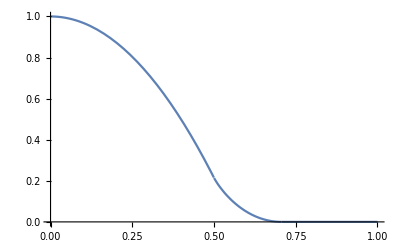

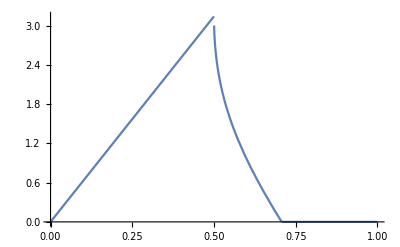

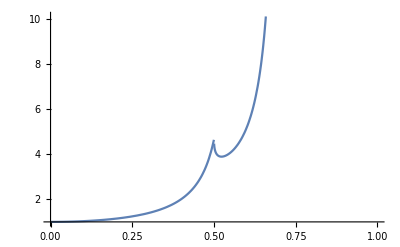

~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Ev.dat

~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Hv.dat

~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Gv.dat

```mathematica
(*Square lattice*)
(*From Torquato, PRE 82, 056109 (2010) and one of my old implementation notebooks*)
(*squareLat_9January2020.nb*)
Clear[Ev,Hv,Gv]
r1=1
rc=Sqrt[2]/2
v1[r_]:=Pi r^2
v2[r_,R_]:=2/Pi v1[R](ArcCos[r/(2R)]-r/(2R)Sqrt[1-r^2/(4R^2)])
Ev[r_]:=Piecewise[{{1-v1[r],r<=r1/2},{1-v1[r]+2v2[r1,r],r1/2<r<rc}}]
Hv=D[-Ev[r],r]
Gv=Hv/(Ev[r]2Pi r)
Plot[Ev[r],{r,0,1}]
Plot[Hv,{r,0,1}]
Plot[Gv,{r,0,1}]

tableUnc=Table[0.0,{r,0.0001,0.7,0.0001}];
tableR=Table[r,{r,0.0001,0.7,0.0001}];
tableEv=Table[Ev[r],{r,0.0001,0.7,0.0001}];
tableHv=Table[N[Hv],{r,0.0001,0.7,0.0001}];
tableGv=Table[N[Gv],{r,0.0001,0.7,0.0001}];

Export["~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Ev.dat",Transpose[{tableR,tableEv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Hv.dat",Transpose[{tableR,tableHv,tableUnc}]]
Export["~/Source_Code/nn_scripts/test/analytical/2D_square_lattice_Gv.dat",Transpose[{tableR,tableGv,tableUnc}]]
```